## reproduction

```mathematica
gra=Item[#,Background->Lighter[Gray, 0.2]]&;
Grid[({{"xNW", "xN", "xNE"}, {"xW", "x", "xE"}, {"xSW", "xS", "xSE"}})/.{"xW"->gra["xW"],"xSW"->gra["xSW"],"xNW"->gra["xNW"]},Frame->All]
```

xNW | xN | xNE
xW | x | xE
xSW | xS | xSE

```mathematica
gra=Item[#,Background->Lighter[Gray, 0.2]]&;
Grid[({{"x'NW", "x'N", "x'NE"}, {"x'W", "x'", "x'E"}, {"x'SW", "x'S", "x'SE"}})/.{"x'"->gra["x'"],"xP_32"->gra["xP_32"],"xP_22"->gra["xP_22"]},Frame->All]
```

x'NW | x'N | x'NE
x'W | x' | x'E
x'SW | x'S | x'SE

```mathematica
lifeVars[]
```

{x,xP,xNW,xN,xNE,xW,xE,xSW,xS,xSE}

```mathematica
lr
```

sat::shdw: Symbol sat appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

plt::shdw: Symbol plt appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
lr;
Clear@@{x,xP,xNW,xN,xNE,xW,xE,xSW,xS,xSE};
Clear[varList];
rules={xP->True,x->False};

the190/.rules;
varList=Complement[
lifeVars[]/.rules,
{True,False}

];
out=sat[varList,the190/.rules,100];
(plt[({{xNW, xN, xNE}, {xW, x, xE}, {xSW, xS, xSE}})/.Thread[Rule[varList,out[[#]]]]~Join~Boole@rules])&/@Range[Length[out]]
```

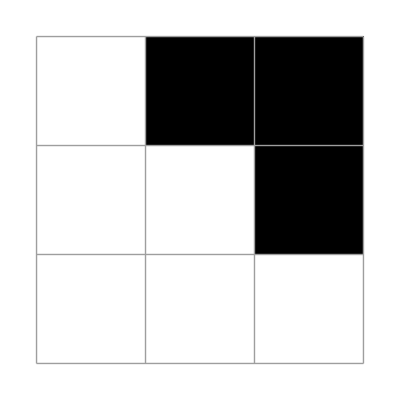
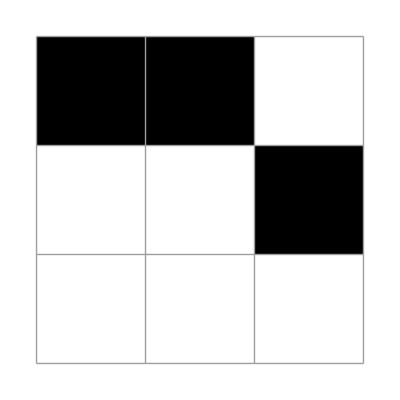
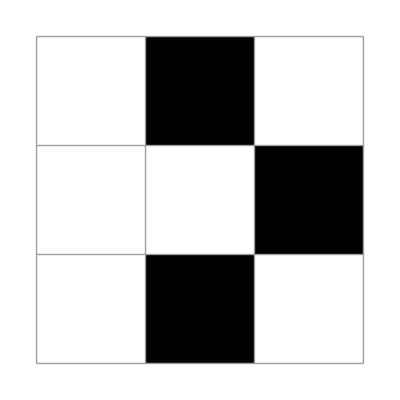
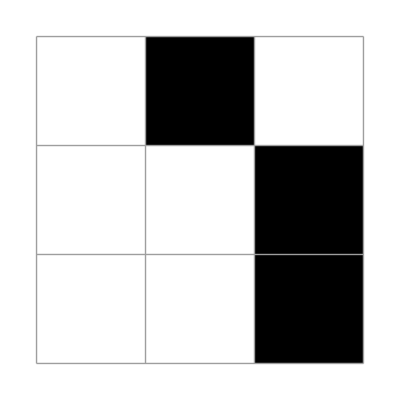
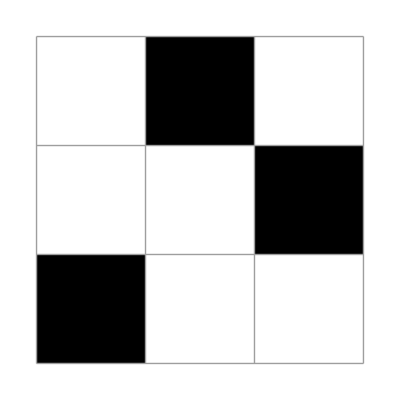
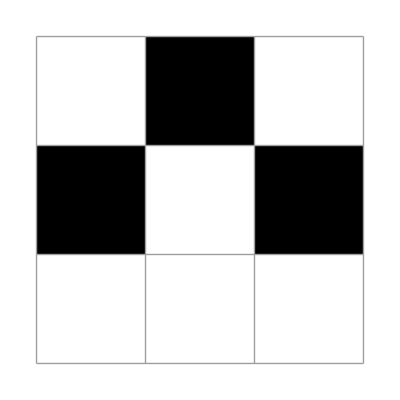
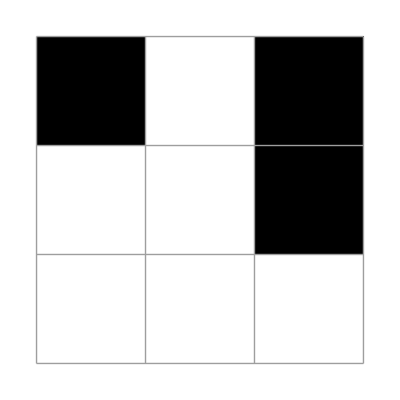
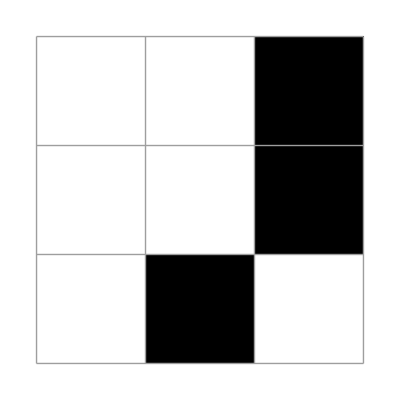
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Length
```

56